### Evolution to more complex self reproduction

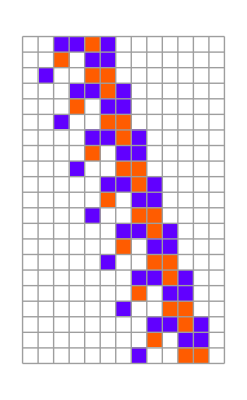

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[{3019941697641,3,1}, {{2,2, 1, 2}, 0}, 20],ColorRules->{0->GrayLevel[1],1->Hue[0.06,1,1],2->Hue[0.73,1,1],3->Hue[0.14,0.81,0.99]}, Mesh->True]
```

```mathematica
cdata90=AssociationThread[Range[15,25],{15,1,15,14,511,12,63,62,2047,8,1023}];

cdata30=AssociationThread[Range[15,25],{1455,6016,10846,2844,247,3420,597,3256,38249,185040,588425}];

GraphicsColumn[Labeled[GraphicsRow[Table[Labeled[RulePlot[CellularAutomaton[#],CenterArray[{1},n],160,ImageSize->{Automatic,300}],Text[Style["size "<>IntegerString[n]<>"\n"<>StringTemplate["(period ``)"][If[#==90,cdata90[n],cdata30[n]]],Italic,7,TextAlignment->Center]],ImageSize->{Automatic,310}],{n,15,25}],ImageSize->550],Framed[Text@Style[StringTemplate["rule ``"][#],Italic]],Left,ImageSize->555]&/@{90,30},ImageSize->650]
```

```mathematica
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[{#,{3,1}},RandomInteger[2,104],{60,{-52,52}}],FrameLabel->{None,StringTemplate["code ``"][#]}]&/@Range[1002,1097,3],4]]
```

```mathematica
FindRepeat[Total/@CellularAutomaton[{3019941697641,3,1}, {{2,2, 1, 2}, 0}, 20]]
```

{7,5,4}